# CellsInsidePolygon Example

```mathematica
<<Cellzilla2D.m
```

Warning: Cellzilla2D: xSSA.m not found in path. Some stochastic conversion functions may not work as expected. It should be loaded manually before any xSSA (stochastic) simulations can be run.

Cellzilla2D (3.0.51 (05 June 2017)) loaded Tue 6 Jun 2017 14:06:26
using xCellerator 0.95 and XSSA ** Not Found **
GPL License Terms Apply

### Define a tissue and a collection of points that define the vertices of a polygon

```mathematica
T=TemplateRandomSquareGrid[100, {-10,-10}, {10,10}];
```

```mathematica
points=Table[{7.*Cos[x], 10.*Sin[x]}, {x,0,(11/6)*Pi, Pi/6}]
```

{{7.,0.},{6.06218,5.},{3.5,8.66025},{0.,10.},{-3.5,8.66025},{-6.06218,5.},{-7.,0.},{-6.06218,-5.},{-3.5,-8.66025},{0.,-10.},{3.5,-8.66025},{6.06218,-5.}}

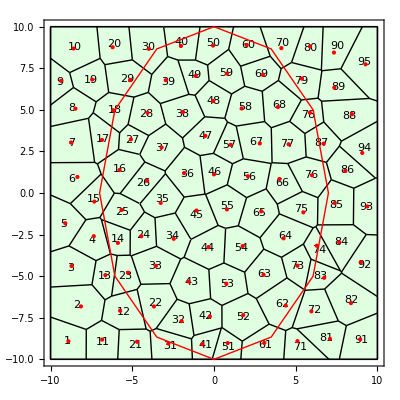

```mathematica
ShowTissue[T,"CellNumbers"-> True,  Frame-> True, Epilog-> {Red,Thick, Point[Centeroid[T]],  Line[Append[points, points[[1]]]]}]
```

### Extract a tissue that contains the points whose center is INSIDE the polygon

```mathematica
Q=CellsInsidePolygon[T, points]
```

{14,16,22,23,24,25,26,27,28,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,62,63,64,65,66,67,68,69,73,74,75,76,77,78}